```mathematica
m=1;
me=5.11*10^-4;
mμ=0.10566;
GeV=1/(1.97*10^-16*m);
ΓX[gSe_,mX_]:=1/3 gSe^2/(4π)mX(1+2 me^2/mX^2)√(1-4 me^2/mX^2)GeV;
Distance[gSe_,mX_,P_]:=P/ΓX[gSe,mX] 1/mX;
```

```mathematica
P[γ_,mX_]:=mX √(γ^2-1);
Prob[gSe_,mX_,γ_]:=ⅇ^(-0.02/Distance[gSe,mX,P[γ,mX]])-ⅇ^(-0.145/Distance[gSe,mX,P[γ,mX]]);
```

```mathematica
Distance[1.0*10^-4,0.1,10]
```

0.000742673

```mathematica
e=0.303;
1.0*10^-4/e
```

0.000330033

```mathematica
Distance[]
```

General::munfl: Exp[-780.927] is too small to represent as a normalized machine number; precision may be lost.

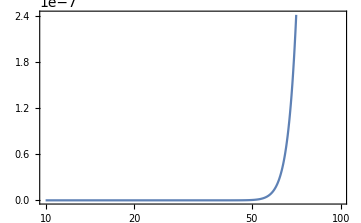

```mathematica
LogLinearPlot[Prob[0.303*10^-4,0.2,p],{p,10,100}]
```

```mathematica
Distance[0.303*10^-4,0.01,1]
```

0.0808965

General::munfl: Exp[-1301.33] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1794.94] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-13013.3] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

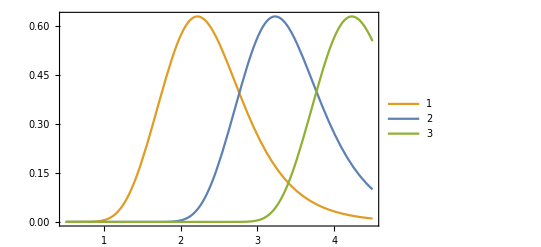

```mathematica
decay=Plot[{Prob[10^-4,0.002,10^logγ],Prob[10^-4,0.02,10^logγ],Prob[10^-4,0.2,10^logγ]},{logγ,0.5,4.5},PlotLegends->Automatic,PlotStyle->{{ColorData[97,2]},{ColorData[97,1]},{ColorData[97,3]}}]
```

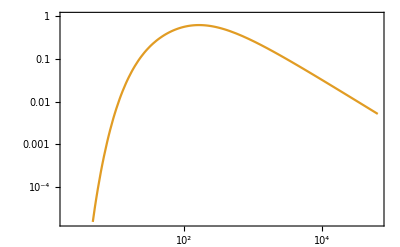

```mathematica
decay1=LogPlot[Prob[10^-4,0.002,10^logγ],{logγ,0.45,4.8},FrameTicks->{{True,None},{myTicks[0,5,1],None}},PlotStyle->ColorData[97,2],PlotRange->{{0.3,4.8},{Log10[3*10^-5],1}}]
```

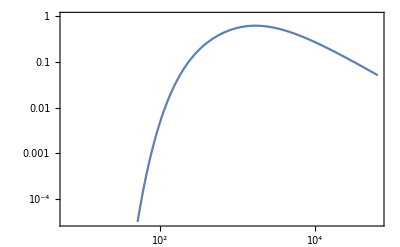

```mathematica
decay2=LogPlot[Prob[10^-4,0.02,10^logγ],{logγ,0.8,4.8},FrameTicks->{{True,None},{myTicks[0,5,1],None}},PlotStyle->ColorData[97,1],PlotRange->{{0.8,4.8},{10^-4.5,1}}]
```

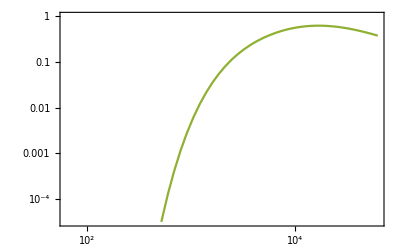

```mathematica
decay3=LogPlot[Prob[10^-4,0.2,10^logγ],{logγ,1.8,4.8},FrameTicks->{{True,None},{myTicks[0,5,1],None}},PlotStyle->ColorData[97,3],PlotRange->{{1.8,4.8},{10^-4.5,1}}]
```